# Chapter 3

## Setup

```mathematica
Unprotect[DivisorSigma];

DivisorSigma[m_Integer]:=DivisorSigma[1,m];
SyntaxInformation[DivisorSigma]={"ArgumentsPattern"->{_,_.}};
Format[HoldPattern[DivisorSigma[m_]],TraditionalForm]:=
σ[m];

Protect[DivisorSigma];
```

```mathematica
Attributes[DivisorTau]=Listable;

DivisorTau[n_Integer]:=
DivisorSigma[0,n];

Format[DivisorTau,TraditionalForm]=τ;
```

```mathematica
PerfectNumberQ[n_]:=
DivisorSigma[n]===2*n;
```

```mathematica
ClearAll[MersenneExponent];
MersenneExponent[1]=2;
MersenneExponent[n_Integer?Positive]:=MersenneExponent[n]=
Module[{p=NextPrime[MersenneExponent[n-1]]},
While[!PrimeQ[2^p-1],
p=NextPrime[p]];
p];

ClearAll[MersennePrime];
MersennePrime[n_Integer?Positive]:=MersennePrime[n]=2^MersenneExponent[n]-1;

Attributes[MersennePrime]=Listable;
```

```mathematica
PrimesTo[x_?Positive]:=Prime@Range@PrimePi@x;
PrimesTo[x_?NumericQ]/;Im[x]==0={};
```

## Introduction

```mathematica
MersenneExponent[4]
```

7

```mathematica
perfects=2^(MersenneExponent[#]-1)*MersennePrime[#]&/@Range[20];
```

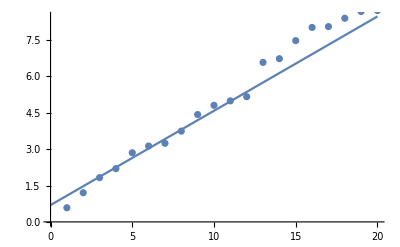

```mathematica
Show[
Plot[Log[2]*Exp[-EulerGamma]*x+Log[2],{x,0,20}],
ListPlot[Log[Log[perfects]]]]
```

## Section 3.1

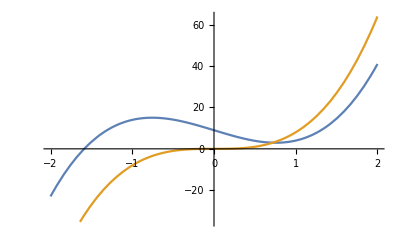

```mathematica
Plot[{7x^3-12x+9,8x^3},{x,-2,2}]
```

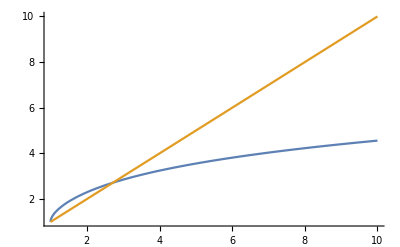

```mathematica
Plot[{Exp[Sqrt[Log[x]]],x},{x,1,10},PlotRange->{0,All}]
```

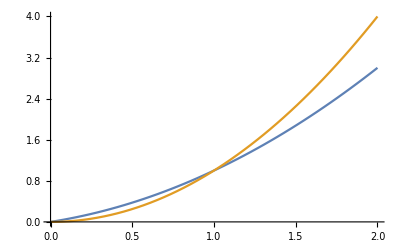

```mathematica
Plot[{n(n+1)/2,n^2},{n,0,2}]
```

```mathematica
Solve[n*(n+1)/2==n^2,n]
```

{{n→0},{n→1}}

### Exercise 3.1.1

Too easy.

### Exercise 3.1.2

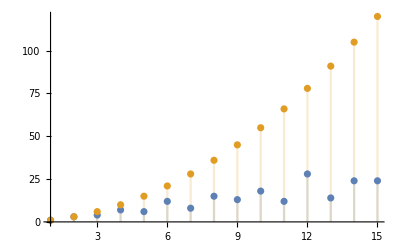

```mathematica
DiscretePlot[{DivisorSigma[n],n*(n+1)/2},{n,1,15}]
```

For m==(p_1^k_1 | … | p_n^k_n),

σ(m)==∏_(j=1)^n p_j^k_j==∏_(j=1)^n (p_j^(k_j+1)-1)/(p_j-1)

We could write

σ(m)==∑_(k=1)^m k Boole[k∣m]≤∑_(k=1)^m k==1/2 k (k+1)

### Exercise 3.1.3

τ(m)==∑_(k=1)^m Boole[k∣m]==∑_(k=1)^m Boole[m/k∣m]

Consider all divisors d of m. If d∣m and d<√m, then √m<m/d. Noting that if m is a perfect square, we’ll be double-counting √m,

τ(m)≤∑_(1≤k≤√m) (Boole[m/k∣m]+Boole[k∣m])==2 ∑_(1≤k≤√m) Boole[k∣m]≤2 ∑_(1≤k≤√m) 1≤2 √m

### Exercise 3.1.4

#### x/(x+1)

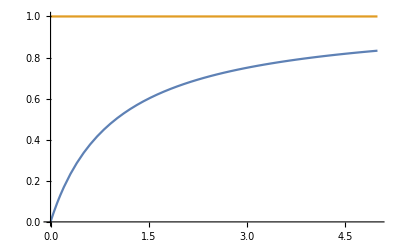

```mathematica
Plot[{x/(x+1),1},{x,0,5}]
```

```mathematica
(x/(x+1)-1)//Together
```

-1/(1+x)

Abs[-1/(x+1)]≤Abs[1/x]

#### cosh(x)

```mathematica
Simplify[Cosh[x]-Exp[x]/2]
```

ⅇ^-x/2

### Exercise 3.1.5

```mathematica
Sum[k^2,{k,1,n}]-n^3/3//Together
```

1/6 (n+3 n^2)

## Section 3.2

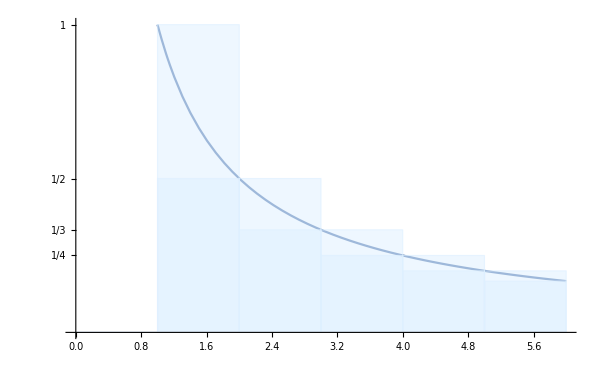

```mathematica
Show[
Plot[1/x,{x,1,6},AxesOrigin->{0,0}],

RectangleChart[{Prepend[Thread[{1,1/Range[1,5]}],{1,0}]},
BarSpacing->0,ChartStyle->Directive[{Opacity[0.5],LightBlue}]
],

RectangleChart[{Prepend[Thread[{1,1/Range[2,6]}],{1,0}]},
BarSpacing->0,ChartStyle->Directive[{Opacity[0.5],LightBlue}]
],

Ticks->{Automatic,1/Range[1,4]},

GridLines->{None,1/Range[1,6]},

ImageSize->600
]
```

### Exercise 3.2.1

0<n-log(n)<1⇒log(n)<n<log(n)+1

Just add log(n) to everything.

### Euler’s constant

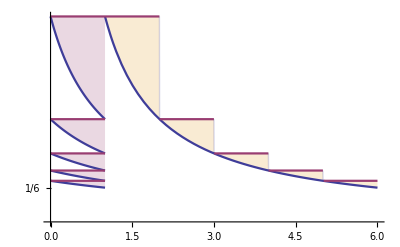

```mathematica
Show[
Plot[{1/x,1/Floor[x]},
{x,1,6},ExclusionsStyle->{Dashed},
AxesOrigin->{0,0},
Filling->{2->{1}},
PlotStyle->ColorData[1]
],

Plot[Evaluate[{1/(x+#),1/Floor[(x+#)]}&/@Range[1,5]],{x,0,1},
PlotStyle->{ColorData[1,1],ColorData[1,2]},

Filling->Table[2*k->{2*k-1},{k,1,6}]
],

Ticks->{Automatic,{1/6}},

GridLines->{None,{1/6}}
]
```

### Exercise 3.2.2

0<n-log(n)-ℽ<1/n

#### 1000

```mathematica
N[Log[1000]+EulerGamma,4]
```

7.485

Check:

```mathematica
N[HarmonicNumber[1000]]
```

7.48547

#### 10000

```mathematica
N[Log[10000]+EulerGamma,5]
```

9.7876

Check:

```mathematica
N[HarmonicNumber[10000]]
```

9.78761

#### 100000

```mathematica
N[Log[100000]+EulerGamma,6]
```

12.0901

Check:

```mathematica
N[HarmonicNumber[100000],20]
```

12.090146129863427947

### Exercise 3.2.3

```mathematica
table=Array[
{HoldForm[10^#],N[HarmonicNumber[10^#],20],N[Log[10^#]+EulerGamma+1/(2*10^#),20]}&,
5]
```

{{10^1,2.9289682539682539683,2.9298007578955785446},{10^2,5.1873775176396202608,5.1873858508896242286},{10^3,7.4854708605503449127,7.4854709438836699127},{10^4,9.7876060360443822642,9.7876060368777155967},{10^5,12.090146129863427947,12.090146129871761281}}

```mathematica
TableForm[table,TableHeadings->{None,{n,HarmonicNumber[n],Log[n]+EulerGamma+1/(2*n)}//Map[TraditionalForm]}]
```

n | n | 1/(2 n)+log(n)+ℽ
10^1 | 2.9289682539682539683 | 2.9298007578955785446
10^2 | 5.1873775176396202608 | 5.1873858508896242286
10^3 | 7.4854708605503449127 | 7.4854709438836699127
10^4 | 9.7876060360443822642 | 9.7876060368777155967
10^5 | 12.090146129863427947 | 12.090146129871761281

```mathematica
-(Subtract@@@table[[All,{2,3}]])
```

{0.0008325039273245764,8.333250003968×10^-6,8.3333325×10^-8,8.33333333×10^-10,8.333333×10^-12}

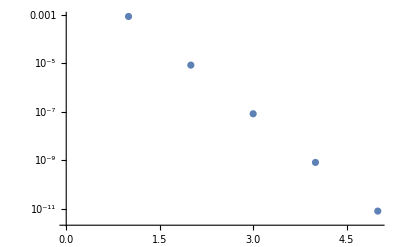

```mathematica
ListLogPlot[-(Subtract@@@table[[All,{2,3}]])]
```

```mathematica
1/12//N
```

0.0833333

```mathematica
-(Subtract@@@table[[All,{2,3}]])*12*10^Range[2,10,2]
```

{0.9990047127894916,0.9999900004761,0.9999999,0.999999999,1.}

Conjecture:

n==log(n)+ℽ+1/(2 n)-1/(12 n^2)==log(n)+ℽ+1/(2 n)+O(1/n^2)

### Exercise 3.2.4

```mathematica
approx=Function[n,Log[n]+EulerGamma+1/(2*n)-1/(12*n^2)];
```

```mathematica
With[{n:=10^3},
HoldForm[n]]
```

10^3

```mathematica
B[approx[10],20]
```

B[59/1200+EulerGamma+Log[10],20]

```mathematica
row=Function[k,
With[{n:=10^k},
{HoldForm[n],N[HarmonicNumber[n],30],N[approx[n],30]}]];
```

```mathematica
table=Array[row,5];
```

```mathematica
TableForm[table,TableHeadings->{None,{n,HarmonicNumber[n],approx[n]}//Map[TraditionalForm]}]
```

n | n | -1/(12 n^2)+1/(2 n)+log(n)+ℽ
10^1 | 2.92896825396825396825396825397 | 2.92896742456224521129117021143
10^2 | 5.18737751763962026080511767566 | 5.18737751755629089530916166612
10^3 | 7.48547086055034491265651820433 | 7.4854708605503365793271531208
10^4 | 9.78760603604438226417847790485 | 9.78760603604438226334514457549
10^5 | 12.0901461298634279473632193635 | 12.0901461298634279473631360302

```mathematica
(Subtract@@@table[[All,{2,3}]])*120*10^(4*Range[5])
```

{0.99528721050835535765104,0.999952385951472114,0.99999952381002,0.9999999952,1.}

Conjecture:

n==log(n)+ℽ+1/(2 n)-1/(12 n^2)+1/(120 n^4)==log(n)+ℽ+1/(2 n)-1/(12 n^2)+O(1/n^4)

```mathematica
Series[HarmonicNumber[n],{n,Infinity,4}]
```

(EulerGamma-Log[1/n])+1/(2 n)-1/(12 n^2)+1/(120 n^4)+O[1/n]^5

### Exercise 3.3.1

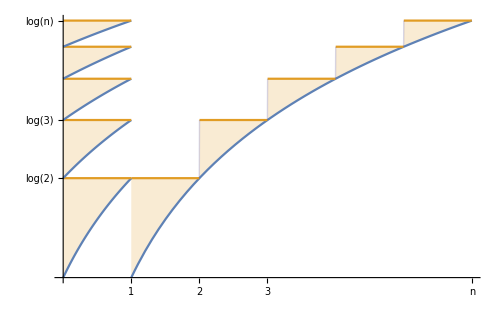

```mathematica
Show[
Plot[{Log[x],Log[Ceiling[x]]},{x,1,6},AxesOrigin->{0,0},
ExclusionsStyle->Medium,Filling->{2->{1}}
],
Sequence@@Array[Plot[{Log[x+#],Log[Ceiling[x+#]]},{x,0,1},
Filling->{2->{1}}
]&,5],

Ticks->{{1,2,3,{Mean@{4,5},SpanFromLeft},{6,n}},{Log[2],Log[3],{Mean[{Log[4],Log[5]}],SpanFromAbove},{Log[6],Log[n]}}},
GridLines->{{1,6},{Log[6]}},
ImageSize->500
]
```

Note that areas between log(k) and log(x) all fit inside a rectangle that is 1×log(n), so the total difference is less than log(n),

### Exercise 3.3.2

We have

log(n!)==n log(n)-n+O(log(n))

or

Abs[log(n!)-n log(n)+n]≪log(n)

n!≃n (n/ⅇ)^n

in some sense.

## Section 3.4

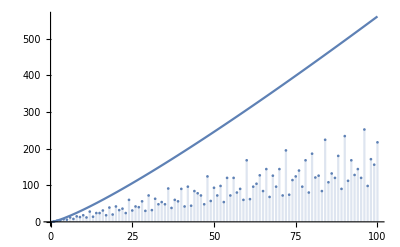

```mathematica
Show[
Plot[n*Log[n]+n,{n,0,100}],
DiscretePlot[
DivisorSigma[n],
{n,1,100}]]
```

### Exercise 3.4.1

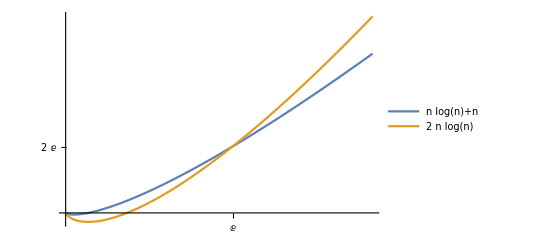

```mathematica
Plot[{n*Log[n]+n,2*n*Log[n]},
{n,0,5},

Ticks->{{E},{2*E}},

GridLines->{{E},{2*E}},

PlotLegends->"Expressions"
]
```

### Exercise 3.4.2

s(n)==σ(n)-n≪n log(n)

## Section 3.5

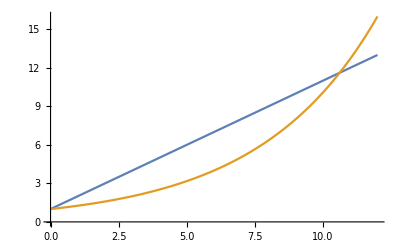

```mathematica
Plot[{t+1,2^(t/3)},{t,0,12}]
```

```mathematica
E^3//N
```

20.0855

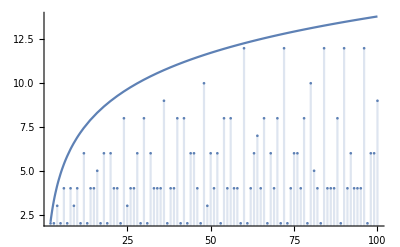

```mathematica
Show[
Plot[3*Log[n],{n,2,100}],

DiscretePlot[DivisorTau[n],{n,1,100}]
]
```

```mathematica
D[Exp[t*Log[p]/3],t]
```

1/3 p^(t/3) Log[p]

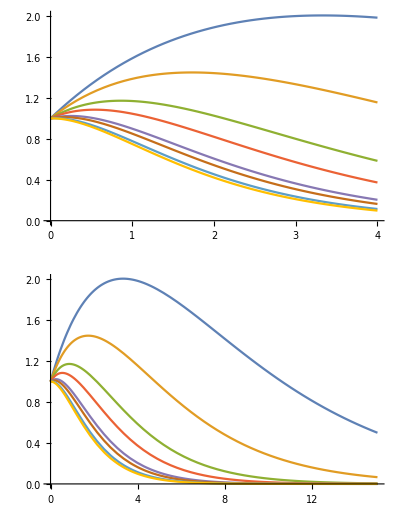

```mathematica
With[{curves=(t+1)*PrimesTo[19]^(-t/3)},
GraphicsColumn[
{Plot[curves,{t,0,4},
GridLines->{Flatten[t/.Solve[D[#,t]==0,t]&/@curves],None}],
Plot[curves,{t,0,15}]}]]
```

```mathematica
FindRoot[
#,{t,1}]&/@
D[(t+1)*PrimesTo[19]^(-t/3),t]
```

{{t→3.32809},{t→1.73072},{t→0.864005},{t→0.541695},{t→0.251097},{t→0.169614},{t→0.0588684},{t→0.0188698}}

### Exercise 3.5.1

```mathematica
deriv=D[(t+1)*p^(-t/3),t]//Factor
```

-1/3 p^(-t/3) (-3+Log[p]+t Log[p])

```mathematica
sol=t/.First@Solve[deriv==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(3-Log[p])/Log[p]

```mathematica
Simplify[sol==3/Log[p]-1]
```

True

```mathematica
sol/.p->PrimesTo[19]
```

{(3-Log[2])/Log[2],(3-Log[3])/Log[3],(3-Log[5])/Log[5],(3-Log[7])/Log[7],(3-Log[11])/Log[11],(3-Log[13])/Log[13],(3-Log[17])/Log[17],(3-Log[19])/Log[19]}

```mathematica
(3-Log[19.])/Log[19.]
```

0.0188698

```mathematica
N[sol/.p->PrimesTo[19]]
```

{3.32809,1.73072,0.864005,0.541695,0.251097,0.169614,0.0588684,0.0188698}

```mathematica
FoldList[Times,%]
```

{3.32809,5.75998,4.97665,2.69582,0.676914,0.114814,0.00675891,0.000127539}

### Exercise 3.5.2

```mathematica
NextPrime[Exp[4]]
```

59

```mathematica
N[Exp[t*Log[59]/4]/.t->5]
```

163.518

```mathematica
D[Exp[t*Log[p]/4],t]
```

1/4 p^(t/4) Log[p]

```mathematica
fun=(t+1)*Exp[-t*Log[p]/4]
```

p^(-t/4) (1+t)

```mathematica
Solve[D[fun,t]==0,t]
```

{{t→(4-Log[p])/Log[p]}}

```mathematica
NextPrime[Exp[4],-1]
```

53

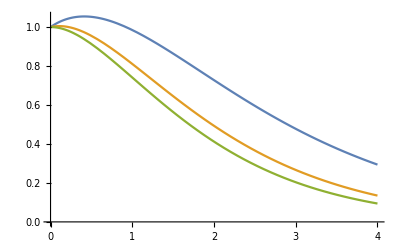

```mathematica
Plot[fun/.p->{17,37,53}//Evaluate,{t,0,4}]
```

```mathematica
t/.First@Solve[D[fun,t]==0,t]/.p->53
```

(4-Log[53])/Log[53]

```mathematica
N[%]
```

0.0074826

## Section 3.6

```mathematica
DivisorSigma[10!]
```

15334088

```mathematica
10!
```

3628800

```mathematica
Log[10!]//N
```

15.1044

### Exercise 3.6.1

s(n)>C (n-1)

### Exercie 3.6.2

```mathematica
𝒩=Ceiling[Exp[2]]
```

8

```mathematica
n=𝒩!
```

40320

```mathematica
2<DivisorSigma[n]/n
```

True

```mathematica
DivisorSigma[12]/12
```

7/3

```mathematica
𝒩=Ceiling[Exp[3]]
```

21

```mathematica
n=𝒩!
```

51090942171709440000

```mathematica
DivisorSigma[n]/n
```

274753126637/47997593280

```mathematica
N[%]
```

5.72431

```mathematica
𝒩=.;n=.
```

```mathematica
?FindInstance
```

FindInstance[expr,vars] finds an instance of vars that makes the statement expr be True. 
FindInstance[expr,vars,dom] finds an instance over the domain dom. Common choices of dom are Complexes, Reals, Integers, and Booleans. 
FindInstance[expr,vars,dom,n] finds n instances.

```mathematica
Module[{n=1},
While[DivisorSigma[n]/n≤3,
++n];
n]
```

180

```mathematica
DivisorSigma[#]-#&@%
```

366

```mathematica
DivisorSigma[59000!]/59000!//N
```

19.5745

### Exercise 3.6.3

```mathematica
Range[7,13,2]!!
```

{105,945,10395,135135}

```mathematica
DivisorSigma[%]
```

{192,1920,23040,322560}

```mathematica
%-%%
```

{87,975,12645,187425}

```mathematica
FullSimplify[Sum[1/d,{d,1,2*𝒩+1,2}],𝒩∈Integers]
```

1/2 HarmonicNumber[1/2+𝒩]+Log[2]

### Exercise 3.6.4

```mathematica
𝒞=2;
𝒩=Ceiling[Exp[2*𝒞]]
```

55

```mathematica
n=(2𝒩+1)!!
```

3853986162502645785712150546541904653309504195240303679678670940619904075006404195556640625

## Section 3.7

### 3.7.1

Let n=p^k for any prime p and any k ≥ 100.

### 3.7.2

Nothing.

### Lemma

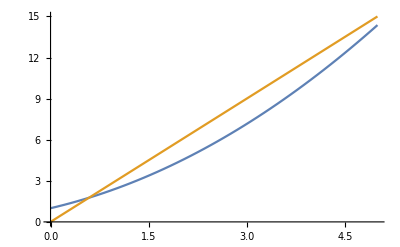

```mathematica
Plot[{(x/Log[6]+1)^2,3x},{x,0,5}]
```

```mathematica
Solve[{(x/Log[6]+1)^2==𝒞*x},x]//Simplify
```

{{x→1/2 Log[6] (-2+𝒞 Log[6]-√𝒞 √Log[6] √(-4+𝒞 Log[6]))},{x→1/2 Log[6] (-2+𝒞 Log[6]+√𝒞 √Log[6] √(-4+𝒞 Log[6]))}}

### 3.7.3

```mathematica
Simplify[DivisorSigma[0,(2*3*5*7)^k],{k∈Integers,0<k}]
```

DivisorSigma[0,210^k]

### 3.7.4

Try n==15^m==2^m×3^m×5^m, so

τ(n)==((log(n))/(log(15))+1)^3

Then we just need to show that

(x/(log(15))+1)^3≤C x^2

is eventually false; since the leading term on the left hand side is proportional to x^3, this is obviously true.